# The H-function

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Analytic Solution

### H-function (Stibbs-Weir)

```mathematica
Clear[H];
H[α_,u_]:=Exp[-u/Pi NIntegrate[Log[1-α t Cot[t]]/(Cos[t]^2+u^2 Sin[t]^2),{t,0,Pi/2}]]
```

### Approximate H-function

Hapke approximation 1

```mathematica
H1[w_,u_]:=(1+2u)/(1+2u √(1-w))
```

Hapke approximation 2

```mathematica
Clear[H2];H2[w_,u_]:=(1-(1-y)u(n+(1-n/2-n u)Log[(1+u)/u]))^-1/.n->(1-y)/(1+y)/.y->(1-w)^(1/2)
```

```mathematica
V[s_,c_]:=1-c/(2 s)Log[(1+s)/(1-s)]
```

```mathematica
vexact[c_?NumericQ]:=FindRoot[V[s,c]==0,{s,10^-10,1-10^-10},Method->"Brent"][[1]][[2]]
```

### Grosjean 1958b approximation

```mathematica
HGrosjean[w_,u_]:=1+(w u)/2 Log[(1+u)/u]+(2 w^2 u)/((1+K u)((13-5w)/8+2/3(2-w)K))-(w^2 u)/((13-5w)/8+2/3(2-w)K)(17/32+15/16 u-u(1+15/16 u)Log[(1+u)/u])/.K->((3(1-w))/(2-w))^(1/2)
```

### NSE 1976 vol 27, 607 - 608 (two more approximations are given)

```mathematica
H32[c_,u_]:=(1-c/2((1-A u+B u^2)u Log[(1+u)/u]+A u + (u/2-u^2)B))^-1//.{A->α-2/3 B,B->(K Log[1+K]+(K+Log[1-K])α)/(K/b+(2/3-1/K)Log[1-K]-1),α->4/c(1-√(1-c))-2,b->1/((√(1-c))/(2K)-c/(4 K^2)Log[1-K^2]),K->vexact[c]}
```

```mathematica
H32[0.5,1]
```

1.24997

### Compare various approximations

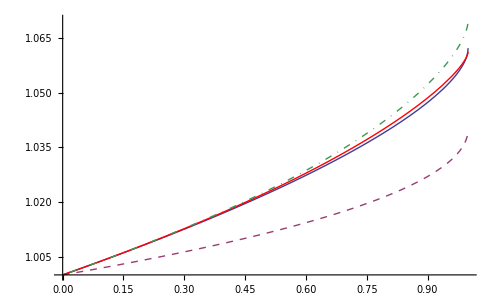

```mathematica
u=0.02;
Plot[
{
H[c,u],
H1[c,u],
H2[c,u],
HGrosjean[c,u]
}
,{c,0,1},PlotStyle->{Thick,Dashed,Red,DotDashed}
]
```

### H-function moments

```mathematica
Hmoment1[c_]:=(1-√(1-c))2/c
```

```mathematica
HmomentApprox[c_,j_]:=1/(j+1)2/(1+y)(1+j/(2(j+2))(1-y)/(1+y))/.y->√(1-c)
```

```mathematica
a
```

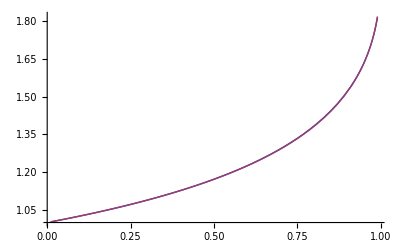

```mathematica
Plot[{
NIntegrate[ H2[c,u],{u,0,1}],
Hmoment1[c]
},{c,0.01,.99}]
```

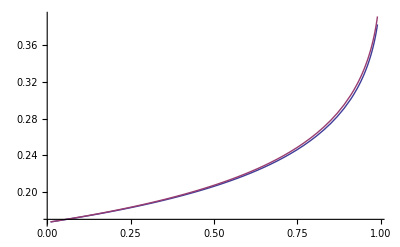

```mathematica
j=5;
Plot[{
NIntegrate[ u^j H2[c,u],{u,0,1}],
HmomentApprox[c,j]
},{c,0.01,.99}]
```

## Benchmark H-function data

```mathematica
Hfuncdata=Table[H[c,u],{c,{0.001,0.01,0.05,0.1,0.2,0.3,0.5,0.7,0.8,0.9,0.95,0.98,0.99,0.995,0.999,0.9999,0.99999,0.999999}},{u,{0.01,0.1,0.2,0.5,1}}];
```

```mathematica
Transpose[Join[{Table[c,{c,{0.001,0.01,0.05,0.1,0.2,0.3,0.5,0.7,0.8,0.9,0.95,0.98,0.99,0.995,0.999,0.9999,0.99999,0.999999}}]},Transpose[Hfuncdata]]];
```

```mathematica
Grid[%]
```

0.001 | 1.00002 | 1.00012 | 1.00018 | 1.00027 | 1.00035
0.01 | 1.00023 | 1.0012 | 1.0018 | 1.00276 | 1.00349
0.05 | 1.00116 | 1.00609 | 1.00914 | 1.01409 | 1.01785
0.1 | 1.00235 | 1.01238 | 1.01864 | 1.02892 | 1.03682
0.2 | 1.00478 | 1.02562 | 1.03892 | 1.06118 | 1.07865
0.3 | 1.0073 | 1.03987 | 1.06115 | 1.09756 | 1.12684
0.5 | 1.01272 | 1.07237 | 1.11346 | 1.18774 | 1.25126
0.7 | 1.01887 | 1.11303 | 1.18252 | 1.31795 | 1.44475
0.8 | 1.02242 | 1.13881 | 1.22864 | 1.41326 | 1.59822
0.9 | 1.0266 | 1.17214 | 1.29143 | 1.55603 | 1.8501
0.95 | 1.02923 | 1.19523 | 1.33734 | 1.67179 | 2.07712
0.98 | 1.03131 | 1.21513 | 1.37876 | 1.78629 | 2.32579
0.99 | 1.03226 | 1.22488 | 1.39977 | 1.8486 | 2.47279
0.995 | 1.03289 | 1.23162 | 1.41463 | 1.89463 | 2.58735
0.999 | 1.03367 | 1.24042 | 1.43442 | 1.95869 | 2.75607
0.9999 | 1.03408 | 1.24518 | 1.44532 | 1.99545 | 2.85822
0.99999 | 1.03421 | 1.24667 | 1.44876 | 2.00728 | 2.89196
0.999999 | 1.03424 | 1.24713 | 1.44985 | 2.01104 | 2.90278